# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Washington"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-03

```mathematica
states=Union[seqData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Alabama→{{2022-01-20,9},{2022-01-21,19},{2022-01-22,26},{2022-01-23,12},{2022-01-24,14},{2022-01-25,12},{2022-01-26,11},{2022-01-27,5},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},Arizona→{{2022-01-20,190},{2022-01-21,369},{2022-01-22,168},{2022-01-23,158},{2022-01-24,549},{2022-01-25,357},{2022-01-26,403},{2022-01-27,439},{2022-01-28,323},{2022-01-29,195},{2022-01-30,105},{2022-01-31,299},{2022-02-01,214},{2022-02-02,222},{2022-02-03,146}},Arkansas→{{2022-01-20,48},{2022-01-21,66},{2022-01-22,5},{2022-01-23,2},{2022-01-24,119},{2022-01-25,69},{2022-01-26,90},{2022-01-27,25},{2022-01-28,1},{2022-01-29,0},{2022-01-30,0},{2022-01-31,1},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},California→{{2022-01-20,406},{2022-01-21,390},{2022-01-22,1118},{2022-01-23,243},{2022-01-24,593},{2022-01-25,641},{2022-01-26,175},{2022-01-27,58},{2022-01-28,48},{2022-01-29,729},{2022-01-30,42},{2022-01-31,49},{2022-02-01,12},{2022-02-02,7},{2022-02-03,0}},Colorado→{{2022-01-20,218},{2022-01-21,140},{2022-01-22,64},{2022-01-23,89},{2022-01-24,140},{2022-01-25,78},{2022-01-26,196},{2022-01-27,88},{2022-01-28,73},{2022-01-29,0},{2022-01-30,0},{2022-01-31,1},{2022-02-01,1},{2022-02-02,1},{2022-02-03,0}},Connecticut→{{2022-01-20,168},{2022-01-21,219},{2022-01-22,61},{2022-01-23,87},{2022-01-24,191},{2022-01-25,166},{2022-01-26,105},{2022-01-27,93},{2022-01-28,48},{2022-01-29,3},{2022-01-30,40},{2022-01-31,95},{2022-02-01,47},{2022-02-02,30},{2022-02-03,51}},Delaware→{{2022-01-20,41},{2022-01-21,40},{2022-01-22,2},{2022-01-23,3},{2022-01-24,5},{2022-01-25,3},{2022-01-26,5},{2022-01-27,7},{2022-01-28,1},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},Florida→{{2022-01-20,152},{2022-01-21,142},{2022-01-22,68},{2022-01-23,20},{2022-01-24,83},{2022-01-25,57},{2022-01-26,26},{2022-01-27,9},{2022-01-28,15},{2022-01-29,13},{2022-01-30,15},{2022-01-31,16},{2022-02-01,13},{2022-02-02,14},{2022-02-03,0}},Georgia→{{2022-01-20,228},{2022-01-21,96},{2022-01-22,31},{2022-01-23,71},{2022-01-24,22},{2022-01-25,130},{2022-01-26,42},{2022-01-27,79},{2022-01-28,26},{2022-01-29,17},{2022-01-30,1},{2022-01-31,53},{2022-02-01,54},{2022-02-02,34},{2022-02-03,0}},Illinois→{{2022-01-20,53},{2022-01-21,72},{2022-01-22,28},{2022-01-23,17},{2022-01-24,63},{2022-01-25,42},{2022-01-26,23},{2022-01-27,6},{2022-01-28,2},{2022-01-29,2},{2022-01-30,1},{2022-01-31,0},{2022-02-01,0},{2022-02-02,1},{2022-02-03,1}},Indiana→{{2022-01-20,104},{2022-01-21,184},{2022-01-22,23},{2022-01-23,11},{2022-01-24,25},{2022-01-25,30},{2022-01-26,45},{2022-01-27,16},{2022-01-28,3},{2022-01-29,1},{2022-01-30,3},{2022-01-31,18},{2022-02-01,9},{2022-02-02,1},{2022-02-03,4}},Louisiana→{{2022-01-20,51},{2022-01-21,90},{2022-01-22,16},{2022-01-23,15},{2022-01-24,86},{2022-01-25,34},{2022-01-26,101},{2022-01-27,30},{2022-01-28,103},{2022-01-29,8},{2022-01-30,0},{2022-01-31,2},{2022-02-01,15},{2022-02-02,35},{2022-02-03,24}},Maryland→{{2022-01-20,132},{2022-01-21,97},{2022-01-22,66},{2022-01-23,30},{2022-01-24,30},{2022-01-25,34},{2022-01-26,35},{2022-01-27,22},{2022-01-28,7},{2022-01-29,14},{2022-01-30,15},{2022-01-31,14},{2022-02-01,9},{2022-02-02,14},{2022-02-03,0}},Massachusetts→{{2022-01-20,767},{2022-01-21,465},{2022-01-22,420},{2022-01-23,952},{2022-01-24,1268},{2022-01-25,829},{2022-01-26,773},{2022-01-27,704},{2022-01-28,492},{2022-01-29,25},{2022-01-30,284},{2022-01-31,401},{2022-02-01,399},{2022-02-02,138},{2022-02-03,453}},Michigan→{{2022-01-20,88},{2022-01-21,59},{2022-01-22,28},{2022-01-23,27},{2022-01-24,78},{2022-01-25,53},{2022-01-26,48},{2022-01-27,31},{2022-01-28,19},{2022-01-29,10},{2022-01-30,8},{2022-01-31,12},{2022-02-01,7},{2022-02-02,0},{2022-02-03,0}},Minnesota→{{2022-01-20,136},{2022-01-21,143},{2022-01-22,144},{2022-01-23,57},{2022-01-24,59},{2022-01-25,37},{2022-01-26,27},{2022-01-27,157},{2022-01-28,25},{2022-01-29,20},{2022-01-30,18},{2022-01-31,26},{2022-02-01,6},{2022-02-02,1},{2022-02-03,1}},Nebraska→{{2022-01-20,104},{2022-01-21,94},{2022-01-22,55},{2022-01-23,7},{2022-01-24,151},{2022-01-25,172},{2022-01-26,76},{2022-01-27,69},{2022-01-28,31},{2022-01-29,20},{2022-01-30,27},{2022-01-31,50},{2022-02-01,23},{2022-02-02,23},{2022-02-03,30}},Nevada→{{2022-01-20,139},{2022-01-21,93},{2022-01-22,12},{2022-01-23,5},{2022-01-24,74},{2022-01-25,93},{2022-01-26,28},{2022-01-27,12},{2022-01-28,21},{2022-01-29,3},{2022-01-30,7},{2022-01-31,33},{2022-02-01,21},{2022-02-02,16},{2022-02-03,24}},New Hampshire→{{2022-01-20,41},{2022-01-21,49},{2022-01-22,15},{2022-01-23,11},{2022-01-24,84},{2022-01-25,27},{2022-01-26,27},{2022-01-27,32},{2022-01-28,42},{2022-01-29,1},{2022-01-30,0},{2022-01-31,9},{2022-02-01,15},{2022-02-02,3},{2022-02-03,10}},New Jersey→{{2022-01-20,45},{2022-01-21,49},{2022-01-22,49},{2022-01-23,22},{2022-01-24,43},{2022-01-25,111},{2022-01-26,124},{2022-01-27,122},{2022-01-28,18},{2022-01-29,3},{2022-01-30,0},{2022-01-31,23},{2022-02-01,5},{2022-02-02,3},{2022-02-03,0}},New Mexico→{{2022-01-20,165},{2022-01-21,27},{2022-01-22,12},{2022-01-23,9},{2022-01-24,10},{2022-01-25,11},{2022-01-26,13},{2022-01-27,12},{2022-01-28,2},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,1},{2022-02-03,1}},New York→{{2022-01-20,480},{2022-01-21,358},{2022-01-22,223},{2022-01-23,182},{2022-01-24,365},{2022-01-25,316},{2022-01-26,244},{2022-01-27,240},{2022-01-28,150},{2022-01-29,16},{2022-01-30,20},{2022-01-31,49},{2022-02-01,41},{2022-02-02,16},{2022-02-03,17}},North Carolina→{{2022-01-20,157},{2022-01-21,105},{2022-01-22,176},{2022-01-23,179},{2022-01-24,257},{2022-01-25,126},{2022-01-26,90},{2022-01-27,174},{2022-01-28,45},{2022-01-29,25},{2022-01-30,26},{2022-01-31,29},{2022-02-01,29},{2022-02-02,28},{2022-02-03,1}},North Dakota→{{2022-01-20,79},{2022-01-21,97},{2022-01-22,57},{2022-01-23,19},{2022-01-24,87},{2022-01-25,52},{2022-01-26,11},{2022-01-27,28},{2022-01-28,92},{2022-01-29,41},{2022-01-30,54},{2022-01-31,36},{2022-02-01,41},{2022-02-02,95},{2022-02-03,28}},Ohio→{{2022-01-20,96},{2022-01-21,119},{2022-01-22,20},{2022-01-23,11},{2022-01-24,103},{2022-01-25,50},{2022-01-26,43},{2022-01-27,60},{2022-01-28,49},{2022-01-29,0},{2022-01-30,0},{2022-01-31,45},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},Oregon→{{2022-01-20,117},{2022-01-21,120},{2022-01-22,83},{2022-01-23,20},{2022-01-24,57},{2022-01-25,53},{2022-01-26,40},{2022-01-27,25},{2022-01-28,22},{2022-01-29,14},{2022-01-30,6},{2022-01-31,11},{2022-02-01,20},{2022-02-02,1},{2022-02-03,0}},Pennsylvania→{{2022-01-20,98},{2022-01-21,88},{2022-01-22,61},{2022-01-23,51},{2022-01-24,57},{2022-01-25,111},{2022-01-26,35},{2022-01-27,111},{2022-01-28,30},{2022-01-29,18},{2022-01-30,3},{2022-01-31,3},{2022-02-01,11},{2022-02-02,0},{2022-02-03,0}},South Carolina→{{2022-01-20,67},{2022-01-21,16},{2022-01-22,15},{2022-01-23,7},{2022-01-24,15},{2022-01-25,7},{2022-01-26,8},{2022-01-27,7},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},Tennessee→{{2022-01-20,71},{2022-01-21,185},{2022-01-22,67},{2022-01-23,92},{2022-01-24,37},{2022-01-25,35},{2022-01-26,16},{2022-01-27,13},{2022-01-28,15},{2022-01-29,2},{2022-01-30,2},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},Texas→{{2022-01-20,521},{2022-01-21,480},{2022-01-22,518},{2022-01-23,340},{2022-01-24,130},{2022-01-25,142},{2022-01-26,349},{2022-01-27,360},{2022-01-28,239},{2022-01-29,166},{2022-01-30,0},{2022-01-31,1},{2022-02-01,1},{2022-02-02,0},{2022-02-03,0}},Utah→{{2022-01-20,260},{2022-01-21,286},{2022-01-22,155},{2022-01-23,61},{2022-01-24,299},{2022-01-25,189},{2022-01-26,134},{2022-01-27,162},{2022-01-28,120},{2022-01-29,54},{2022-01-30,12},{2022-01-31,95},{2022-02-01,66},{2022-02-02,129},{2022-02-03,22}},Vermont→{{2022-01-20,131},{2022-01-21,128},{2022-01-22,218},{2022-01-23,84},{2022-01-24,167},{2022-01-25,91},{2022-01-26,118},{2022-01-27,28},{2022-01-28,108},{2022-01-29,121},{2022-01-30,9},{2022-01-31,181},{2022-02-01,80},{2022-02-02,0},{2022-02-03,90}},Virginia→{{2022-01-20,21},{2022-01-21,18},{2022-01-22,7},{2022-01-23,5},{2022-01-24,12},{2022-01-25,6},{2022-01-26,22},{2022-01-27,18},{2022-01-28,0},{2022-01-29,0},{2022-01-30,0},{2022-01-31,0},{2022-02-01,0},{2022-02-02,0},{2022-02-03,0}},Wisconsin→{{2022-01-20,87},{2022-01-21,83},{2022-01-22,35},{2022-01-23,22},{2022-01-24,34},{2022-01-25,47},{2022-01-26,104},{2022-01-27,62},{2022-01-28,63},{2022-01-29,24},{2022-01-30,11},{2022-01-31,11},{2022-02-01,6},{2022-02-02,11},{2022-02-03,1}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

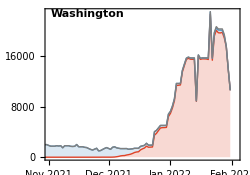

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

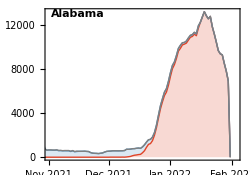
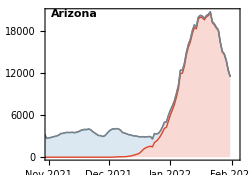
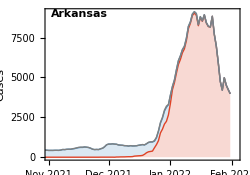
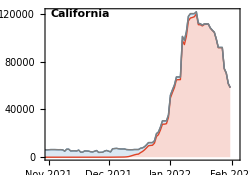
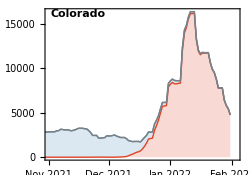
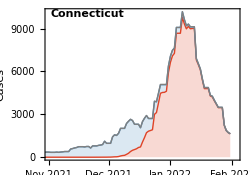
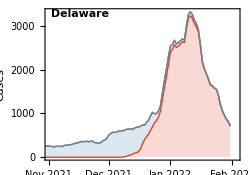
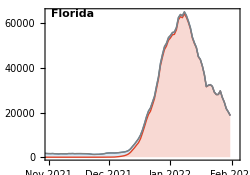
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png